```mathematica
Directory[]
```

/Users/alexis/workspace/clustersearch/cpp/build

```mathematica
SetDirectory["/Users/alexis/workspace/clustersearch/cpp/build"]
```

/Users/alexis/workspace/clustersearch/cpp/build

This function wraps the program “clusters”

```mathematica
Clusters[alpha_,length_,colors_,gray_,samples_]:=
(* Returns means of cluster_size, perimeter_size, colors, exits_size, robustness *)
Block[{args,command,seed=0},
args="";
args = StringJoin[args," ", "--alpha=",     ToString[alpha]];
args = StringJoin[args," ", "--length=",   ToString[length]];
args = StringJoin[args," ", "--colors=",   ToString[colors]];
args = StringJoin[args," ", "--gray=",       ToString[gray]];
args = StringJoin[args," ", "--samples=", ToString[samples]];
args = StringJoin[args," ", "--seed=",       ToString[seed]];
args = StringJoin[args," ", "--verbose=0"];
command=StringJoin["!./clusters",args];
Flatten @ ReadList[command,Number,RecordLists->True]]
```

For example, we can search one cluster given binary length-10 strings with 4 colors:.

```mathematica
Clusters[2,10,4,0,1]
```

{240,691,3,1718,0.284167}

These help with displaying tabular output from multiple calls to Clusters

```mathematica
(* Headings of Clusters output, for labelling tabular displays.

For example:
 TableForm[<output>,TableHeadings->{None,ClustersHeadingsShort},TableAlignments->"."];
   Grid[%129~Prepend~ClustersHeadingsShort,Alignment->"."];
 *)
ClustersHeadingsShort=
{"s","t","E","u","r"};
ClustersHeadingsLong={"cluster_size","perimeter_size","colors_seen","exits_size","robustness"};
```

```mathematica
ClustersTableForm[table_]:=
TableForm[table,TableHeadings->{None,ClustersHeadingsShort},TableAlignments->"."]
```

An example

Suppose that I want to
hold constant
   alpha =2
   length=10 
   samples = 15
   gray=0

let 
  colors range from 2 to 5,
 
and generate a table of  outputs from Clusters

```mathematica
(* Generate table ranging over colors from 2..5 *)
With[{alpha=2,length=8,samples=100,gray=0},
Table[Clusters[alpha,length,colors,gray,samples],
{colors,2,5}]]
```

{{126.58,125.85,1,503.58,0.496301},{74.45,148.44,2,386.32,0.325612},{38.43,112.36,2.99,215.6,0.237349},{15.93,62.35,3.96,93.76,0.191666}}

Display it as a table with headings

```mathematica
ClustersTableForm[%]
```

s | t | E | u | r
126.58 | 125.85 | 1 | 503.58 | 0.496301
74.45 | 148.44 | 2 | 386.32 | 0.325612
38.43 | 112.36 | 2.99 | 215.6 | 0.237349
15.93 | 62.35 | 3.96 | 93.76 | 0.191666

Suppose I want to generate the same table as below, but left-joining a column of colors

```mathematica
(* Generate table ranging over colors from 2..5 *)
With[{alpha=2,length=8,samples=10,gray=0},
Table[{colors}~Join~Clusters[alpha,length,colors,gray,samples],
{colors,2,5}]]
```

{{2,126.9,127.7,1,508,0.497934},{3,66.6,132.9,2,347.4,0.294298},{4,44.6,126.6,3,245.4,0.272793},{5,19.1,70.2,3.9,111.2,0.175014}}

Display it as a table with headings, adding a new heading m for colors allowed.

```mathematica
ClustersTableFormRanging[table_,rangeHeader_]:=
(* Clusters output, with a ranging input var in left col *)
TableForm[table,
TableHeadings->{None,{rangeHeader}~Join~ClustersHeadingsShort},
TableAlignments->"."]
```

```mathematica
ClustersTableFormRanging[%%,"m"]
```

m | s | t | E | u | r
2 | 126.9 | 127.7 | 1 | 508 | 0.497934
3 | 66.6 | 132.9 | 2 | 347.4 | 0.294298
4 | 44.6 | 126.6 | 3 | 245.4 | 0.272793
5 | 19.1 | 70.2 | 3.9 | 111.2 | 0.175014

We use this pick out columns to prepare arguments for ListPlot

```mathematica
PickColumn1andCol[table_,col_]:=
(* Picks cols 1 and COL from table *)
Map[( #[[{1,col}]] & ),table]
```

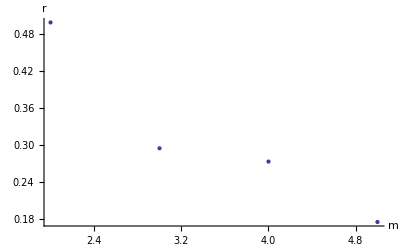

```mathematica
ListPlot[%,AxesLabel->{m,r}]
```

Now let’s do some analysis
ranging 
  colors from 2 ... 32.
with
  length=8
  alpha=2

```mathematica
(* Generate table ranging over colors from 2..5 *)
data = With[{alpha=2,length=8,samples=100,gray=0},
Table[{colors}~Join~Clusters[alpha,length,colors,gray,samples],
{colors,2,32}]]
```

{{2,126.58,125.85,1,503.58,0.496301},{3,74.45,148.44,2,386.32,0.325612},{4,38.43,112.36,2.99,215.6,0.237349},{5,15.93,62.35,3.96,93.76,0.191666},{6,9.57,43.08,4.77,57.82,0.15834},{7,5.94,29.71,5.44,37.04,0.130381},{8,5.11,26.54,6.18,32.22,0.119144},{9,3.53,20.12,6.46,22.96,0.105911},{10,2.9,17.28,6.79,19.28,0.0867411},{11,2.53,15.68,7.25,17.02,0.0863608},{12,2.37,15.07,7.38,16.18,0.0794941},{13,1.92,12.82,7.47,13.48,0.0621012},{14,2.08,13.7,8.04,14.44,0.0762817},{15,1.92,12.93,8.18,13.46,0.0699792},{16,1.96,13.11,8.11,13.72,0.0673056},{17,1.75,12.11,8.19,12.5,0.0588512},{18,1.65,11.52,7.97,11.9,0.0493125},{19,1.5,10.76,7.85,11,0.0410417},{20,1.67,11.6,8.34,12,0.0501012},{21,1.87,12.68,9.06,13.2,0.0645357},{22,1.45,10.46,8.15,10.7,0.0396042},{23,1.35,9.99,7.91,10.1,0.0340833},{24,1.54,11.06,8.59,11.24,0.0522083},{25,1.35,9.98,8.27,10.1,0.0347083},{26,1.25,9.43,8,9.5,0.02575},{27,1.41,10.32,8.51,10.44,0.0397917},{28,1.44,10.47,8.83,10.62,0.041375},{29,1.39,10.17,8.48,10.34,0.0344345},{30,1.27,9.56,8.19,9.6,0.0289583},{31,1.27,9.56,8.19,9.62,0.0279167},{32,1.34,9.91,8.5,10.02,0.0322917}}

```mathematica
(* Generate table ranging over colors from 2..5 *)
bigdata = 
Table[
{gray,
With[{alpha=2,length=8,samples=1000,gray=gray},
Table[{colors}~Join~Clusters[alpha,length,colors,gray,samples],
{colors,2,64,2}]]},
{gray,0.1,1,0.1}];
```

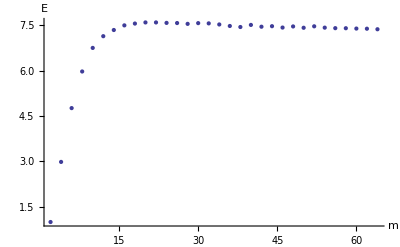

```mathematica
With[
{grayvalue=0.2,
valueindex=4,
valuelabel="E"},
Module[
{grayindex =Position[(#[[1]]&) /@ bigdata,grayvalue][[1,1]],
plottable},
plottable = PickColumn1andCol[bigdata[[grayindex]][[2]],valueindex];
ListPlot[plottable,AxesLabel->{m,valuelabel}]]]
```

```mathematica
Position[(#[[1]]&) /@ bigdata,.2][[1,1]]
```

2

```mathematica
bigdata
```

{{0.1,{{2,230.617,25.383,1,183.16,0.90032},{4,62.91,143.752,2.979,338.124,0.295362},{6,12.469,52.648,4.754,74.554,0.179216},{8,4.667,25.145,6.146,29.652,0.128032},{10,2.986,17.925,7.055,19.792,0.102084},{12,2.356,15.038,7.534,16.076,0.0839904},{14,2.01,13.372,7.899,14.028,0.0727029},{16,1.807,12.383,8.054,12.82,0.0638043},{18,1.689,11.773,8.212,12.116,0.0568929},{20,1.556,11.082,8.179,11.328,0.0488679},{22,1.489,10.738,8.209,10.93,0.0449244},{24,1.44,10.482,8.265,10.632,0.0418792},{26,1.402,10.271,8.253,10.408,0.0382708},{28,1.36,10.035,8.255,10.156,0.0347167},{30,1.324,9.841,8.197,9.94,0.0321625},{32,1.311,9.77,8.216,9.862,0.0309208},{34,1.285,9.622,8.225,9.704,0.0286917},{36,1.263,9.507,8.194,9.578,0.026875},{38,1.244,9.403,8.163,9.462,0.0253458},{40,1.224,9.29,8.121,9.342,0.023575},{42,1.205,9.184,8.068,9.23,0.0218333},{44,1.197,9.14,8.089,9.182,0.0210833},{46,1.19,9.104,8.097,9.14,0.0207292},{48,1.174,9.014,8.064,9.044,0.0191458},{50,1.168,8.977,8.085,9.008,0.0183958},{52,1.162,8.945,8.029,8.972,0.018},{54,1.153,8.895,8.041,8.918,0.0172292},{56,1.145,8.848,8.018,8.87,0.0163125},{58,1.142,8.83,8.033,8.852,0.0159375},{60,1.137,8.803,8.009,8.822,0.0155},{62,1.13,8.761,7.997,8.78,0.0147083},{64,1.127,8.744,7.964,8.762,0.0143333}}},{0.2,{{2,205.185,50.815,1,325.974,0.800622},{4,47.348,127.721,2.984,263.056,0.262129},{6,8.218,38.537,4.76,50.138,0.15889},{8,3.621,20.71,5.969,23.552,0.111332},{10,2.572,16.072,6.747,17.37,0.0914516},{12,2.09,13.762,7.134,14.492,0.0755543},{14,1.834,12.521,7.338,12.98,0.0648647},{16,1.692,11.794,7.491,12.13,0.0572661},{18,1.556,11.082,7.551,11.328,0.0488679},{20,1.482,10.706,7.588,10.888,0.0443851},{22,1.427,10.409,7.588,10.554,0.040775},{24,1.381,10.152,7.573,10.278,0.036625},{26,1.335,9.895,7.568,10.004,0.0325125},{28,1.314,9.788,7.541,9.88,0.0313292},{30,1.29,9.656,7.565,9.736,0.0295167},{32,1.263,9.507,7.557,9.578,0.026875},{34,1.241,9.382,7.521,9.444,0.0247542},{36,1.215,9.243,7.471,9.29,0.0228042},{38,1.2,9.158,7.437,9.2,0.0215417},{40,1.196,9.137,7.506,9.176,0.0212292},{42,1.178,9.035,7.447,9.068,0.0194792},{44,1.169,8.983,7.464,9.014,0.0185208},{46,1.163,8.95,7.419,8.978,0.0180417},{48,1.154,8.897,7.456,8.924,0.0171042},{50,1.145,8.848,7.412,8.87,0.0163125},{52,1.141,8.823,7.46,8.846,0.0158125},{54,1.133,8.778,7.416,8.798,0.0149167},{56,1.129,8.755,7.399,8.774,0.0145833},{58,1.125,8.731,7.397,8.75,0.014},{60,1.121,8.709,7.386,8.726,0.0136667},{62,1.114,8.666,7.381,8.684,0.0127917},{64,1.106,8.62,7.363,8.636,0.011875}}},{0.3,{{2,179.533,76.449,1,428.846,0.700134},{4,31.857,101.228,2.986,181.912,0.23286},{6,5.63,28.75,4.613,35.236,0.134951},{8,2.986,17.925,5.686,19.792,0.102084},{10,2.236,14.471,6.235,15.37,0.0802149},{12,1.876,12.746,6.571,13.234,0.0685227},{14,1.696,11.814,6.688,12.158,0.0578205},{16,1.553,11.064,6.712,11.31,0.0484991},{18,1.464,10.61,6.73,10.774,0.0435815},{20,1.408,10.299,6.778,10.442,0.0385625},{22,1.36,10.035,6.801,10.156,0.0347167},{24,1.317,9.801,6.765,9.898,0.0313708},{26,1.296,9.691,6.805,9.776,0.0295542},{28,1.264,9.512,6.763,9.58,0.0272625},{30,1.24,9.383,6.743,9.438,0.0251167},{32,1.212,9.225,6.73,9.272,0.0224083},{34,1.199,9.151,6.723,9.194,0.0211667},{36,1.19,9.104,6.707,9.14,0.0207292},{38,1.17,8.989,6.693,9.02,0.0186458},{40,1.164,8.956,6.674,8.984,0.0180833},{42,1.154,8.897,6.672,8.924,0.0171042},{44,1.145,8.848,6.659,8.87,0.0163125},{46,1.141,8.823,6.637,8.846,0.0158125},{48,1.13,8.761,6.616,8.78,0.0147083},{50,1.127,8.744,6.618,8.762,0.0143333},{52,1.122,8.716,6.645,8.732,0.013875},{54,1.114,8.666,6.628,8.684,0.0127917},{56,1.106,8.62,6.608,8.636,0.011875},{58,1.105,8.617,6.609,8.63,0.012},{60,1.102,8.598,6.593,8.612,0.0115417},{62,1.098,8.574,6.625,8.588,0.0111458},{64,1.097,8.569,6.599,8.582,0.0111042}}},{0.4,{{2,153.783,101.814,1,489.626,0.599938},{4,18.566,70.221,2.957,108.898,0.198499},{6,4.044,22.553,4.416,25.998,0.120423},{8,2.496,15.702,5.248,16.912,0.0888172},{10,1.946,13.084,5.612,13.648,0.0704611},{12,1.713,11.891,5.801,12.25,0.0582806},{14,1.546,11.033,5.858,11.264,0.0483997},{16,1.451,10.533,5.892,10.696,0.042275},{18,1.391,10.207,5.914,10.338,0.0373958},{20,1.328,9.867,5.927,9.964,0.0326292},{22,1.305,9.743,5.926,9.826,0.0307792},{24,1.266,9.525,5.911,9.592,0.0275958},{26,1.24,9.383,5.892,9.438,0.0251167},{28,1.207,9.198,5.844,9.242,0.0220833},{30,1.196,9.137,5.877,9.176,0.0212292},{32,1.177,9.028,5.862,9.062,0.0193542},{34,1.167,8.97,5.863,9.002,0.0182708},{36,1.156,8.911,5.845,8.936,0.0173333},{38,1.145,8.848,5.848,8.87,0.0163125},{40,1.138,8.809,5.82,8.828,0.015625},{42,1.13,8.761,5.819,8.78,0.0147083},{44,1.124,8.727,5.827,8.744,0.0140417},{46,1.116,8.679,5.814,8.696,0.0130417},{48,1.108,8.632,5.799,8.648,0.012125},{50,1.104,8.611,5.806,8.624,0.011875},{52,1.1,8.587,5.794,8.6,0.0113958},{54,1.098,8.574,5.799,8.588,0.0111458},{56,1.094,8.551,5.798,8.564,0.0106458},{58,1.09,8.529,5.783,8.54,0.0103958},{60,1.089,8.524,5.781,8.534,0.0102708},{62,1.085,8.5,5.809,8.51,0.00977083},{64,1.083,8.487,5.784,8.498,0.0094375}}},{0.5,{{2,127.6,126.379,1,506.56,0.500124},{4,9.395,42.579,2.902,56.95,0.165464},{6,2.986,17.925,4.13,19.792,0.102084},{8,2.059,13.593,4.673,14.31,0.0738012},{10,1.731,11.989,4.91,12.366,0.0594375},{12,1.534,10.967,5.021,11.198,0.0474241},{14,1.428,10.416,5.045,10.558,0.0410667},{16,1.36,10.035,5.091,10.156,0.0347167},{18,1.313,9.783,5.083,9.874,0.0312875},{20,1.269,9.54,5.075,9.614,0.0273042},{22,1.236,9.359,5.08,9.414,0.0247},{24,1.202,9.171,5.045,9.212,0.021875},{26,1.19,9.104,5.066,9.14,0.0207292},{28,1.169,8.983,5.05,9.014,0.0185208},{30,1.156,8.911,5.044,8.936,0.0173333},{32,1.144,8.841,5.03,8.864,0.0161042},{34,1.136,8.796,5.04,8.816,0.0152917},{36,1.127,8.744,5.031,8.762,0.0143333},{38,1.121,8.709,5.047,8.726,0.0136667},{40,1.108,8.632,5.037,8.648,0.012125},{42,1.104,8.611,5.04,8.624,0.011875},{44,1.099,8.581,5.029,8.594,0.0112708},{46,1.097,8.569,5.024,8.582,0.0111042},{48,1.09,8.529,5.026,8.54,0.0103958},{50,1.089,8.524,5.019,8.534,0.0102708},{52,1.085,8.5,5.044,8.51,0.00977083},{54,1.082,8.482,5.028,8.492,0.00939583},{56,1.077,8.451,5.011,8.462,0.00877083},{58,1.075,8.44,5.021,8.45,0.00852083},{60,1.072,8.424,5.022,8.432,0.0083125},{62,1.071,8.418,5.011,8.426,0.0081875},{64,1.07,8.412,5.012,8.42,0.0080625}}},{0.6,{{2,98.987,146.278,1,465.962,0.400411},{4,5.073,26.668,2.809,31.948,0.132951},{6,2.3,14.756,3.691,15.732,0.0825856},{8,1.764,12.171,4.059,12.56,0.0618713},{10,1.51,10.838,4.161,11.048,0.0455604},{12,1.407,10.3,4.223,10.438,0.0388542},{14,1.323,9.834,4.215,9.936,0.0318708},{16,1.276,9.578,4.269,9.652,0.0280667},{18,1.229,9.317,4.239,9.374,0.0238167},{20,1.197,9.14,4.234,9.182,0.0210833},{22,1.171,8.996,4.247,9.026,0.0187708},{24,1.16,8.931,4.23,8.96,0.01775},{26,1.143,8.836,4.236,8.858,0.0159792},{28,1.13,8.761,4.235,8.78,0.0147083},{30,1.122,8.716,4.236,8.732,0.013875},{32,1.111,8.651,4.237,8.666,0.0125833},{34,1.104,8.611,4.241,8.624,0.011875},{36,1.098,8.574,4.243,8.588,0.0111458},{38,1.092,8.54,4.227,8.552,0.0104792},{40,1.089,8.524,4.224,8.534,0.0102708},{42,1.085,8.5,4.234,8.51,0.00977083},{44,1.082,8.482,4.227,8.492,0.00939583},{46,1.075,8.44,4.214,8.45,0.00852083},{48,1.072,8.424,4.232,8.432,0.0083125},{50,1.071,8.418,4.224,8.426,0.0081875},{52,1.069,8.405,4.225,8.414,0.0079375},{54,1.065,8.384,4.221,8.39,0.007625},{56,1.06,8.356,4.206,8.36,0.00716667},{58,1.056,8.333,4.213,8.336,0.00675},{60,1.053,8.315,4.207,8.318,0.006375},{62,1.052,8.309,4.217,8.312,0.00625},{64,1.05,8.297,4.213,8.3,0.006}}},{0.7,{{2,62.91,143.752,1,338.124,0.295362},{4,2.986,17.925,2.58,19.792,0.102084},{6,1.807,12.383,3.146,12.82,0.0638043},{8,1.489,10.738,3.282,10.93,0.0449244},{10,1.36,10.035,3.343,10.156,0.0347167},{12,1.285,9.622,3.384,9.704,0.0286917},{14,1.224,9.29,3.393,9.342,0.023575},{16,1.19,9.104,3.411,9.14,0.0207292},{18,1.162,8.945,3.399,8.972,0.018},{20,1.142,8.83,3.415,8.852,0.0159375},{22,1.127,8.744,3.412,8.762,0.0143333},{24,1.114,8.666,3.431,8.684,0.0127917},{26,1.102,8.598,3.423,8.612,0.0115417},{28,1.097,8.569,3.418,8.582,0.0111042},{30,1.089,8.524,3.418,8.534,0.0102708},{32,1.083,8.487,3.417,8.498,0.0094375},{34,1.077,8.451,3.42,8.462,0.00877083},{36,1.072,8.424,3.417,8.432,0.0083125},{38,1.071,8.418,3.432,8.426,0.0081875},{40,1.068,8.402,3.413,8.408,0.008},{42,1.06,8.356,3.414,8.36,0.00716667},{44,1.056,8.333,3.414,8.336,0.00675},{46,1.053,8.315,3.411,8.318,0.006375},{48,1.05,8.297,3.408,8.3,0.006},{50,1.044,8.261,3.403,8.264,0.00525},{52,1.044,8.261,3.408,8.264,0.00525},{54,1.043,8.255,3.412,8.258,0.005125},{56,1.04,8.238,3.395,8.24,0.00483333},{58,1.039,8.233,3.404,8.234,0.00479167},{60,1.037,8.221,3.408,8.222,0.00454167},{62,1.036,8.215,3.41,8.216,0.00441667},{64,1.034,8.203,3.401,8.204,0.00416667}}},{0.8,{{2,18.566,70.221,1,108.898,0.198499},{4,1.946,13.084,2.188,13.648,0.0704611},{6,1.451,10.533,2.427,10.696,0.042275},{8,1.305,9.743,2.508,9.826,0.0307792},{10,1.207,9.198,2.555,9.242,0.0220833},{12,1.167,8.97,2.576,9.002,0.0182708},{14,1.138,8.809,2.584,8.828,0.015625},{16,1.116,8.679,2.603,8.696,0.0130417},{18,1.1,8.587,2.601,8.6,0.0113958},{20,1.09,8.529,2.602,8.54,0.0103958},{22,1.083,8.487,2.601,8.498,0.0094375},{24,1.074,8.436,2.591,8.444,0.0085625},{26,1.07,8.412,2.595,8.42,0.0080625},{28,1.064,8.379,2.594,8.384,0.00758333},{30,1.054,8.321,2.595,8.324,0.0065},{32,1.05,8.297,2.589,8.3,0.006},{34,1.044,8.261,2.594,8.264,0.00525},{36,1.043,8.255,2.597,8.258,0.005125},{38,1.04,8.238,2.594,8.24,0.00483333},{40,1.037,8.221,2.608,8.222,0.00454167},{42,1.036,8.215,2.607,8.216,0.00441667},{44,1.033,8.197,2.611,8.198,0.00404167},{46,1.031,8.185,2.605,8.186,0.00379167},{48,1.031,8.185,2.61,8.186,0.00379167},{50,1.03,8.179,2.609,8.18,0.00366667},{52,1.029,8.173,2.617,8.174,0.00354167},{54,1.028,8.167,2.616,8.168,0.00341667},{56,1.024,8.143,2.613,8.144,0.00291667},{58,1.024,8.143,2.611,8.144,0.00291667},{60,1.024,8.143,2.613,8.144,0.00291667},{62,1.024,8.143,2.608,8.144,0.00291667},{64,1.023,8.137,2.612,8.138,0.00279167}}},{0.9,{{2,2.986,17.925,1,19.792,0.102084},{4,1.36,10.035,1.576,10.156,0.0347167},{6,1.19,9.104,1.69,9.14,0.0207292},{8,1.127,8.744,1.729,8.762,0.0143333},{10,1.097,8.569,1.747,8.582,0.0111042},{12,1.077,8.451,1.74,8.462,0.00877083},{14,1.068,8.402,1.742,8.408,0.008},{16,1.053,8.315,1.758,8.318,0.006375},{18,1.044,8.261,1.755,8.264,0.00525},{20,1.039,8.233,1.758,8.234,0.00479167},{22,1.034,8.203,1.76,8.204,0.00416667},{24,1.031,8.185,1.767,8.186,0.00379167},{26,1.03,8.179,1.768,8.18,0.00366667},{28,1.027,8.161,1.774,8.162,0.00329167},{30,1.024,8.143,1.77,8.144,0.00291667},{32,1.024,8.143,1.772,8.144,0.00291667},{34,1.022,8.131,1.772,8.132,0.00266667},{36,1.022,8.131,1.775,8.132,0.00266667},{38,1.022,8.131,1.777,8.132,0.00266667},{40,1.021,8.125,1.776,8.126,0.00254167},{42,1.019,8.113,1.779,8.114,0.00229167},{44,1.018,8.107,1.779,8.108,0.00216667},{46,1.018,8.107,1.778,8.108,0.00216667},{48,1.017,8.101,1.776,8.102,0.00204167},{50,1.016,8.095,1.778,8.096,0.00191667},{52,1.016,8.095,1.777,8.096,0.00191667},{54,1.016,8.095,1.778,8.096,0.00191667},{56,1.016,8.095,1.778,8.096,0.00191667},{58,1.016,8.095,1.781,8.096,0.00191667},{60,1.016,8.095,1.778,8.096,0.00191667},{62,1.016,8.095,1.778,8.096,0.00191667},{64,1.016,8.095,1.777,8.096,0.00191667}}},{1.,{{2,1,8,1,8,0},{4,1,8,1,8,0},{6,1,8,1,8,0},{8,1,8,1,8,0},{10,1,8,1,8,0},{12,1,8,1,8,0},{14,1,8,1,8,0},{16,1,8,1,8,0},{18,1,8,1,8,0},{20,1,8,1,8,0},{22,1,8,1,8,0},{24,1,8,1,8,0},{26,1,8,1,8,0},{28,1,8,1,8,0},{30,1,8,1,8,0},{32,1,8,1,8,0},{34,1,8,1,8,0},{36,1,8,1,8,0},{38,1,8,1,8,0},{40,1,8,1,8,0},{42,1,8,1,8,0},{44,1,8,1,8,0},{46,1,8,1,8,0},{48,1,8,1,8,0},{50,1,8,1,8,0},{52,1,8,1,8,0},{54,1,8,1,8,0},{56,1,8,1,8,0},{58,1,8,1,8,0},{60,1,8,1,8,0},{62,1,8,1,8,0},{64,1,8,1,8,0}}}}

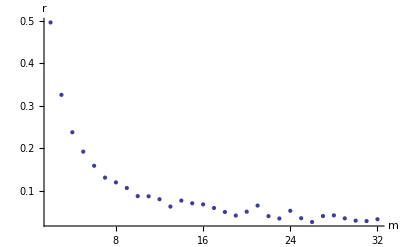

```mathematica
ListPlot[PickColumn1andCol[%247,6],AxesLabel->{m,r}]
```

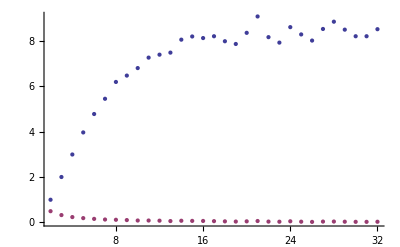

```mathematica
ListPlot[
With[
{data=data
(*
With[{alpha=2,length=8,samples=100,gray=0},
Table[{colors}~Join~Clusters[alpha,length,colors,gray,samples],
{colors,2,32}]]
*)
},
List[
PickColumn1andCol[data,4],
PickColumn1andCol[data,6]]],
AxesLabel->{m}
]
```

```mathematica
Range[2,32] // Length
```

31

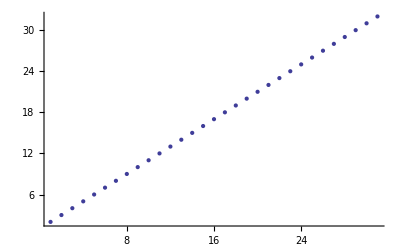

```mathematica
ListPlot[Range[2,32]]
```

```mathematica
Sqrt[Range[40]]
```

{1,√2,√3,2,√5,√6,√7,2 √2,3,√10,√11,2 √3,√13,√14,√15,4,√17,3 √2,√19,2 √5,√21,√22,√23,2 √6,5,√26,3 √3,2 √7,√29,√30,√31,4 √2,√33,√34,√35,6,√37,√38,√39,2 √10}

```mathematica
?Sqrt
```

Sqrt[z] or √z gives the square root of z.

```mathematica
bidata = Table[{k,PDF[BinomialDistribution[50,p],k]},{p,{0.3,0.5,0.8}},{k,0,50}] ;
```

```mathematica
bidata[[2]] // TableForm
```

0 | 8.88178×10^-16
1 | 4.44089×10^-14
2 | 1.08802×10^-12
3 | 1.74083×10^-11
4 | 2.04547×10^-10
5 | 1.88184×10^-9
6 | 1.41138×10^-8
7 | 8.87152×10^-8
8 | 4.76844×10^-7
9 | 2.22527×10^-6
10 | 9.12362×10^-6
11 | 0.0000331768
12 | 0.000107825
13 | 0.000315179
14 | 0.000832974
15 | 0.00199914
16 | 0.00437311
17 | 0.00874623
18 | 0.0160348
19 | 0.0270059
20 | 0.0418591
21 | 0.0597988
22 | 0.0788257
23 | 0.0959617
24 | 0.107957
25 | 0.112275
26 | 0.107957
27 | 0.0959617
28 | 0.0788257
29 | 0.0597988
30 | 0.0418591
31 | 0.0270059
32 | 0.0160348
33 | 0.00874623
34 | 0.00437311
35 | 0.00199914
36 | 0.000832974
37 | 0.000315179
38 | 0.000107825
39 | 0.0000331768
40 | 9.12362×10^-6
41 | 2.22527×10^-6
42 | 4.76844×10^-7
43 | 8.87152×10^-8
44 | 1.41138×10^-8
45 | 1.88184×10^-9
46 | 2.04547×10^-10
47 | 1.74083×10^-11
48 | 1.08802×10^-12
49 | 4.44089×10^-14
50 | 8.88178×10^-16